## BootStrap

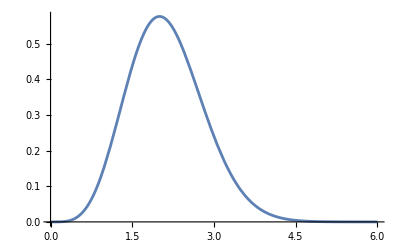

```mathematica
distOrig=Plot[PDF[ChiDistribution[5],x],{x,0,6}]
```

```mathematica
datos=RandomVariate[ChiDistribution[5],100];
```

```mathematica
Length@datos
```

100

```mathematica
dists=FindDistribution[datos,10,All]
```

```mathematica
SortBy[FindDistribution[datos,10,"PearsonChiSquare"],Last]//Reverse
```

{{ChiDistribution[4.87227],0.972125},{GammaDistribution[9.44247,0.221112],0.617715},{NormalDistribution[2.08785,0.682662],0.594915},{LogisticDistribution[2.04552,0.384084],0.527205},{WeibullDistribution[3.24234,2.3287],0.505087},{LogNormalDistribution[0.682248,0.332497],0.483293},{WeibullDistribution[1.99123,1.47278,0.781299],0.440873},{StudentTDistribution[2.06821,0.646318,18.9432],0.440873},{InverseGaussianDistribution[2.08785,17.9104],0.420334},{LaplaceDistribution[2.08785,0.531549],0.092966}}

```mathematica
SortBy[FindDistribution[datos,10,"LogLikelihood"],Last]//Reverse
```

{{WeibullDistribution[1.99123,1.47278,0.781299],-0.949588},{GammaDistribution[9.44247,0.221112],-0.957517},{InverseGaussianDistribution[2.08785,17.9104],-0.960268},{LogNormalDistribution[0.682248,0.332497],-0.960861},{ChiDistribution[4.87227],-0.969676},{StudentTDistribution[2.06821,0.646318,18.9432],-0.994445},{NormalDistribution[2.08785,0.682662],-0.995454},{WeibullDistribution[3.24234,2.3287],-0.997209},{LogisticDistribution[2.04552,0.384084],-0.997494},{LaplaceDistribution[2.08785,0.531549],-1.02401}}

```mathematica
loglik=LogLikelihood[NormalDistribution[μ,σ],datos]//FullSimplify
```

-91.8939-239.937/σ^2+((209.951-50. μ) μ)/σ^2-100. Log[σ]

```mathematica
Plot3D[loglik,{μ,-1,4},{σ,0.01,2},PlotPoints->50]
```

-Graphics3D-

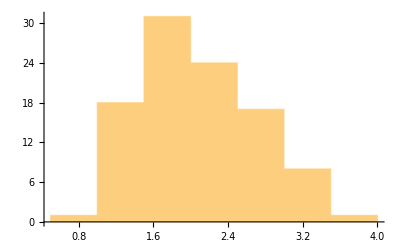

```mathematica
Histogram[datos]
```

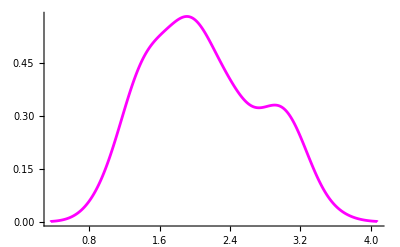

```mathematica
kdedatos=SmoothHistogram[datos,PlotStyle->Magenta]
```

```mathematica
masdatos=RandomChoice[datos,{1000,100}];
```

```mathematica
Dimensions[masdatos]
```

{1000,100}

```mathematica
AbsoluteTiming[sols=FindMaximum[LogLikelihood[NormalDistribution[μ,σ],#],{{μ,2.05},{σ,.71}},Method->"Newton"]& /@ masdatos;//Quiet]
```

{0.773249,Null}

```mathematica
sols[[1;;10]]//TableForm
```

-95.4856 | μ→2.0803
σ→0.628712
-102.445 | μ→2.10225
σ→0.674023
-100.438 | μ→2.08076
σ→0.660632
-94.3028 | μ→2.07144
σ→0.621319
-89.4943 | μ→1.97279
σ→0.59215
-95.758 | μ→2.10129
σ→0.630427
-93.2521 | μ→2.12164
σ→0.614825
-99.9706 | μ→2.03549
σ→0.657552
-101.913 | μ→2.2079
σ→0.67045
-83.6939 | μ→2.09201
σ→0.55878

```mathematica
sols[[1;;5,2]]
```

{{μ→2.0803,σ→0.628712},{μ→2.10225,σ→0.674023},{μ→2.08076,σ→0.660632},{μ→2.07144,σ→0.621319},{μ→1.97279,σ→0.59215}}

```mathematica
mues=μ/.sols[[All,2]];
```

```mathematica
Length@mues
```

1000

```mathematica
sigs=σ/.sols[[All,2]];
```

```mathematica
Length@sigs
```

1000

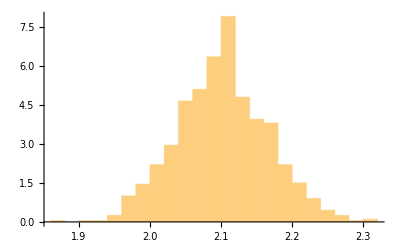

```mathematica
Histogram[mues,Automatic,"PDF"]
```

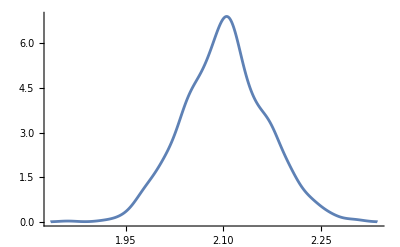

```mathematica
SmoothHistogram[mues,PlotRange->All]
```

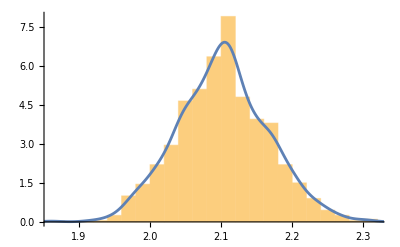

```mathematica
Show[%%,%]
```

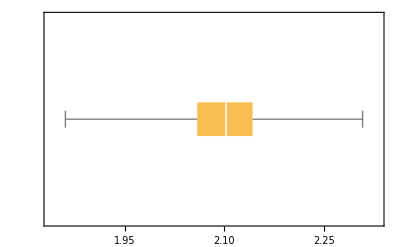

```mathematica
BoxWhiskerChart[mues,BarOrigin->Left]
```

```mathematica
Mean[mues]
```

2.10207

```mathematica
StandardDeviation[mues]
```

0.0637983

```mathematica
Quantile[mues,{0.025,0.975}]
```

{1.97853,2.23169}

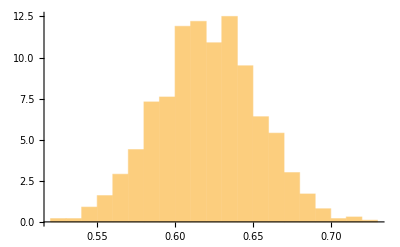

```mathematica
Histogram[sigs,Automatic,"PDF"]
```

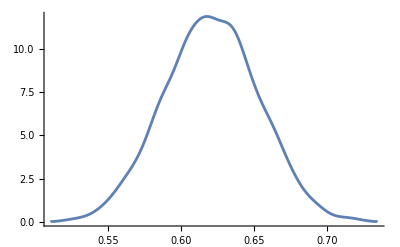

```mathematica
SmoothHistogram[sigs,PlotRange->All]
```

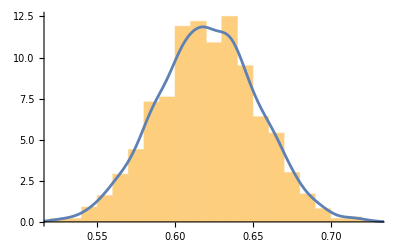

```mathematica
Show[%%,%]
```

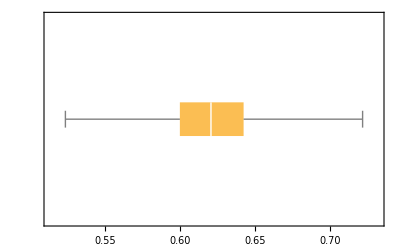

```mathematica
BoxWhiskerChart[sigs,BarOrigin->Left]
```

```mathematica
Mean[sigs]
```

0.620866

```mathematica
StandardDeviation[sigs]
```

0.0321265

```mathematica
Quantile[sigs,{0.025,0.975}]
```

{0.55878,0.681809}

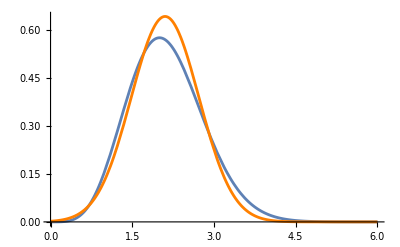

```mathematica
Show[distOrig,Plot[PDF[NormalDistribution[Mean[mues],Mean[sigs]],x],{x,0,6},PlotStyle->Orange],PlotRange->All]
```

### Ejercicio : repetir este ultimo ejemplo con jackknife

Ajuste con NormalDistribution

```mathematica
jacdat=Table[Drop[datos,{k}],{k,Length@datos}];
```

```mathematica
Dimensions@jacdat
```

{100,99}

```mathematica
AbsoluteTiming[solsk=FindMaximum[LogLikelihood[NormalDistribution[μ,σ],#],{{μ,2.05},{σ,.71}},Method->"Newton"]& /@ jacdat;//Quiet]
```

{0.117547,Null}

```mathematica
mues=μ/.solsk[[All,2]];
```

```mathematica
Length@mues
```

100

```mathematica
sigs=σ/.solsk[[All,2]];
```

```mathematica
Length@sigs
```

100

```mathematica
Histogram[mues,Automatic,"PDF"];
```

```mathematica
SmoothHistogram[mues,PlotRange->All];
```

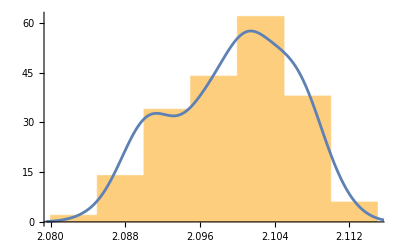

```mathematica
Show[%%,%]
```

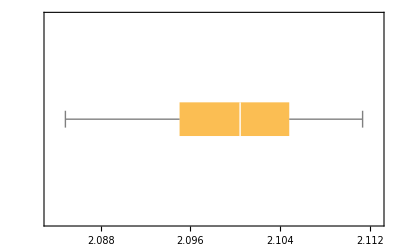

```mathematica
BoxWhiskerChart[mues,BarOrigin->Left]
```

```mathematica
Mean[mues]
```

2.09951

```mathematica
StandardDeviation[mues]
```

0.00634644

```mathematica
Quantile[mues,{0.025,0.975}]
```

{2.08791,2.11026}

```mathematica
Histogram[sigs,Automatic,"PDF"];
```

```mathematica
SmoothHistogram[sigs,PlotRange->All];
```

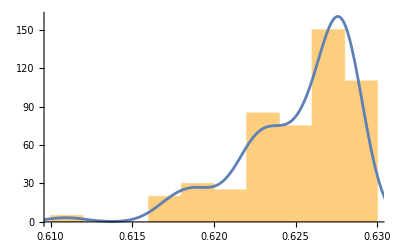

```mathematica
Show[%%,%]
```

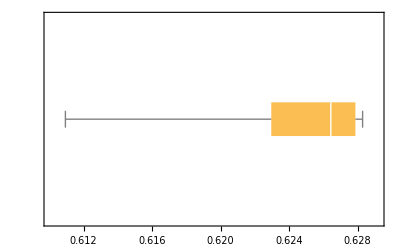

```mathematica
BoxWhiskerChart[sigs,BarOrigin->Left]
```

```mathematica
Mean[sigs]
```

0.625107

```mathematica
StandardDeviation[sigs]
```

0.00342529

```mathematica
Quantile[sigs,{0.025,0.975}]
```

{0.617484,0.628293}

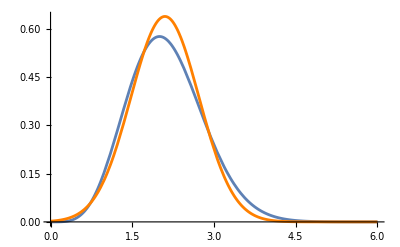

```mathematica
Show[distOrig,Plot[PDF[NormalDistribution[Mean[mues],Mean[sigs]],x],{x,0,6},PlotStyle->Orange],PlotRange->All]
```

Usando la distribucion Chi

```mathematica
AbsoluteTiming[solsk=FindMaximum[LogLikelihood[ChiDistribution[ν],#],{ν}]& /@ jacdat;//Quiet]
```

{0.059084,Null}

```mathematica
nues=ν/.solsk[[All,2]]
```

{4.97701,4.9484,4.98569,4.95386,4.94807,4.94633,5.00032,4.95086,5.01637,4.99337,4.97734,4.95357,5.00195,4.96466,5.01404,4.9439,4.97328,5.0019,4.98244,4.94729,4.96119,5.00041,4.99259,4.97532,4.99365,4.97324,4.9406,4.99194,4.94116,4.97065,5.02501,4.97823,5.01415,4.96592,4.9599,5.016,4.97848,5.01883,4.99596,5.00103,4.9829,4.96373,4.98407,4.98693,4.96564,4.99673,4.96528,5.03666,4.99788,4.9473,4.97252,4.94938,5.03453,4.96248,4.98556,4.94855,5.00777,5.01376,5.01637,4.99947,5.01263,4.94062,5.0008,4.98351,4.96712,4.97791,5.01808,4.96343,5.00872,4.94728,4.94309,5.01002,4.98056,4.98593,5.008,4.95974,4.96921,4.98452,4.95099,4.99369,4.98844,4.9422,4.98184,4.97372,4.98266,4.94333,5.04387,4.95523,4.93336,4.98028,4.96628,4.95555,4.987,4.976,4.94888,4.97946,4.9645,5.00669,4.98157,5.01616}

```mathematica
promν=Mean[nues]
```

4.98005

```mathematica
Histogram[nues,Automatic,"PDF"];
```

```mathematica
SmoothHistogram[nues,PlotRange->All];
```

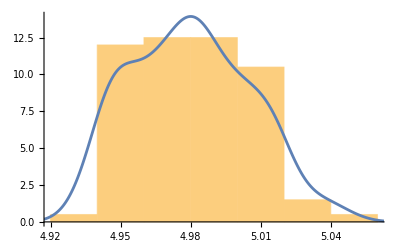

```mathematica
Show[%%,%]
```

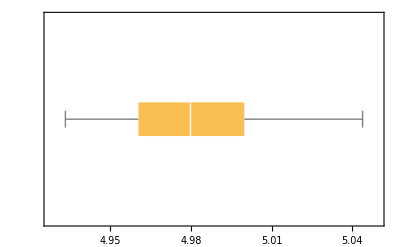

```mathematica
BoxWhiskerChart[nues,BarOrigin->Left]
```

```mathematica
Mean[nues]
```

4.98005

```mathematica
StandardDeviation[nues]
```

0.0253863

```mathematica
Quantile[nues,{0.025,0.975}]
```

{4.94062,5.03453}

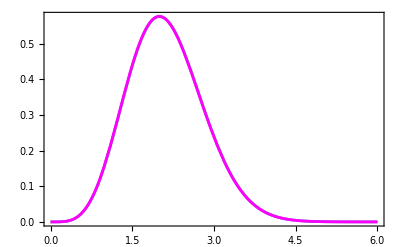

```mathematica
Show[Plot[PDF[ChiDistribution[5],x],{x,0,6},Frame->True],Plot[PDF[ChiDistribution[promν],x],{x,0,6},Frame->True,PlotStyle->Magenta]]
```

## Ejercicio 2: 2 set de datos / correlación.

Se intenta ajustar una función a dos variables (esperablemente) dependientes. 
En este caso, comprobar la Tercera Ley de Kepler (T.b2 ∝ D.b3):

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2024/Clases

```mathematica
exopl=Import["exoplanetas-11-2024.csv"];
```

```mathematica
header2=exopl[[1]]
```

{name,planet_status,mass,mass_error_min,mass_error_max,mass_sini,mass_sini_error_min,mass_sini_error_max,radius,radius_error_min,radius_error_max,orbital_period,orbital_period_error_min,orbital_period_error_max,semi_major_axis,semi_major_axis_error_min,semi_major_axis_error_max,eccentricity,eccentricity_error_min,eccentricity_error_max,inclination,inclination_error_min,inclination_error_max,angular_distance,discovered,updated,omega,omega_error_min,omega_error_max,tperi,tperi_error_min,tperi_error_max,tconj,tconj_error_min,tconj_error_max,tzero_tr,tzero_tr_error_min,tzero_tr_error_max,tzero_tr_sec,tzero_tr_sec_error_min,tzero_tr_sec_error_max,lambda_angle,lambda_angle_error_min,lambda_angle_error_max,impact_parameter,impact_parameter_error_min,impact_parameter_error_max,tzero_vr,tzero_vr_error_min,tzero_vr_error_max,k,k_error_min,k_error_max,temp_calculated,temp_calculated_error_min,temp_calculated_error_max,temp_measured,hot_point_lon,geometric_albedo,geometric_albedo_error_min,geometric_albedo_error_max,log_g,publication,detection_type,mass_measurement_type,radius_measurement_type,alternate_names,molecules,star_name,ra,dec,mag_v,mag_i,mag_j,mag_h,mag_k,star_distance,star_distance_error_min,star_distance_error_max,star_metallicity,star_metallicity_error_min,star_metallicity_error_max,star_mass,star_mass_error_min,star_mass_error_max,star_radius,star_radius_error_min,star_radius_error_max,star_sp_type,star_age,star_age_error_min,star_age_error_max,star_teff,star_teff_error_min,star_teff_error_max,star_detected_disc,star_magnetic_field,star_alternate_names}

```mathematica
Position[header2,"semi_major_axis"]
Position[header2,"orbital_period"]
```

{{15}}

{{12}}

```mathematica
orbdist=Select[exopl,NumberQ[#[[12]]]&&NumberQ[#[[15]]]&][[All,{12,15}]];
```

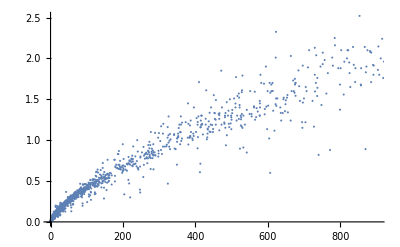

```mathematica
orbDvsT=ListPlot[orbdist]
```

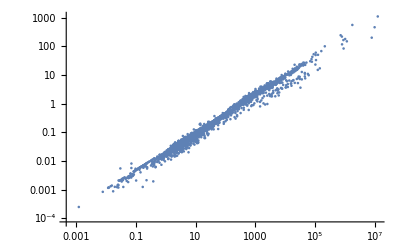

```mathematica
ListLogLogPlot[orbdist]
```

```mathematica
nlf=Fit[Log@orbdist,{1,x},x]
```

-3.97849+0.664651 x

```mathematica
nlf2=NonlinearModelFit[orbdist,a x^n,{n,a},x]
```

FittedModel[…]

```mathematica
PowerExpand@N@Log10@Normal[nlf2]
```

0.434294 (-3.29972+0.60679 Log[x])

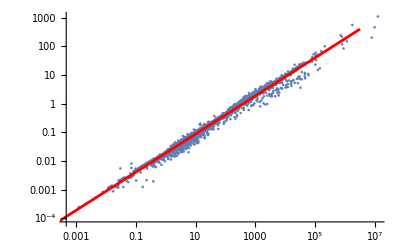

```mathematica
Show[
ListLogLogPlot[orbdist],
Plot[nlf,{x,-10,15},PlotStyle->Red]]
```

```mathematica
nlf1=E^nlf/.x->Log@x
```

0.0187139 x^0.664651

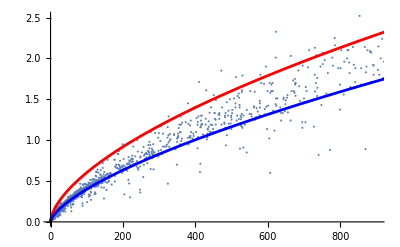

```mathematica
Show[
ListPlot[orbdist],
Plot[nlf2//Normal,{x,0,1000},PlotStyle->Red],
Plot[nlf1,{x,0,1000},PlotStyle->Blue]
]
```

### Estimación del error de los parametros

```mathematica
Length@orbdist
```

4476

```mathematica
masdatos=RandomChoice[orbdist,{1000,Length@orbdist}];
```

```mathematica
AbsoluteTiming[nlfs=Fit[Log10@#,{1,x},x]&/@masdatos;]
```

{0.290207,Null}

```mathematica
nlfs[[1;;3]][[1,2]]
```

0.663654 x

```mathematica
interceptos=nlfs[[All,1]];
```

```mathematica
pendientes=nlfs[[All,2,1]];
```

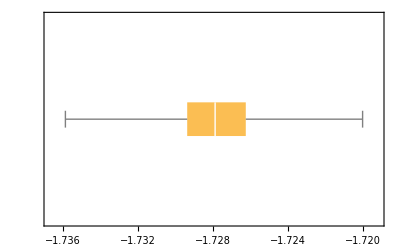

```mathematica
BoxWhiskerChart[interceptos,BarOrigin->Left]
```

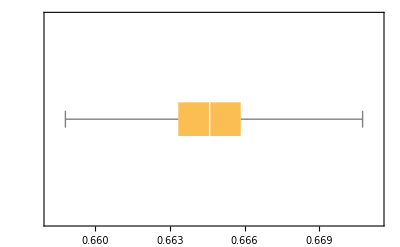

```mathematica
BoxWhiskerChart[pendientes,BarOrigin->Left]
```

```mathematica
Mean[interceptos]
```

-1.72778

```mathematica
Quantile[interceptos,{0.025,0.975}]
```

{-1.73247,-1.72295}

```mathematica
inter=Around[Mean[interceptos],{Mean[interceptos]-Quantile[interceptos,{0.025}],Quantile[interceptos,{0.975}]-Mean[interceptos]}]
```

-1.72778{0.00468199}{0.00483481}

```mathematica
Mean[pendientes]
```

0.664606

```mathematica
Quantile[pendientes,{0.025,0.975}]
```

{0.660947,0.668109}

```mathematica
slope=Around[Mean[pendientes],{Mean[pendientes]-Quantile[pendientes,{0.025}],Quantile[pendientes,{0.975}]-Mean[pendientes]}]
```

0.664606{0.0036587}{0.003503}